```mathematica
δ=(vr^2-vt^2+2 μ (vt-vr))/(4 d);

PL=Exp[δ] ParabolicCylinderD[-s,(μ-vr)/Sqrt[d]]/ParabolicCylinderD[-s,(μ-vt)/Sqrt[d]];

param={μ->0.8,vr->0,vt->1,d->0.1};


Finv=1/(PL);
g=Series[Finv,{s,0,5}]/.param






Roots [1/ParabolicCylinderD[-s,(μ-vt)/Sqrt[d]]==0,s]


(*c1=SeriesCoefficient[Finv,{s,0,5},1]/.param
c2=SeriesCoefficient[Finv,{s,0,5},2]/.param
c3=SeriesCoefficient[Finv,{s,0,5},3]/.param
c4=SeriesCoefficient[Finv,{s,0,5},4]/.param
c5=SeriesCoefficient[Finv,{s,0,5},5]/.param*)
```

1.+2.69165 s+1.97565 s^2+0.633915 s^3+0.111347 s^4+0.0123021 s^5+O[s]^6

Roots::neq: 1/ParabolicCylinderD[-s,(-vt+μ)/(√d)] is expected to be a polynomial in the variable s.

Roots[1/ParabolicCylinderD[-s,(-vt+μ)/(√d)]==0,s]

```mathematica
(*polynome[s_]=1.+c1*s+c2*s^2+c3*s^3+c4*s^4+c5*s^5*)
```

```mathematica
polynome[s_]=1.+2.6916505735477836*s+1.9756458016144234*s^2+0.6339151382287227*s^3+0.11134669232740416*s^4 +0.012302123274705586*s^5
```

```mathematica
Roots[polynome[s]==1,s]
```

s==0||s==-2.82063-1.30995 ⅈ||s==-2.82063+1.30995 ⅈ||s==-1.70487-4.44017 ⅈ||s==-1.70487+4.44017 ⅈ

```mathematica
Roots[polynome[s]==0,s]
```

s==-2.43534-0.534107 ⅈ||s==-2.43534+0.534107 ⅈ||s==-1.80453-4.43098 ⅈ||s==-1.80453+4.43098 ⅈ||s==-0.571289

```mathematica
ll=a+I*b;
```

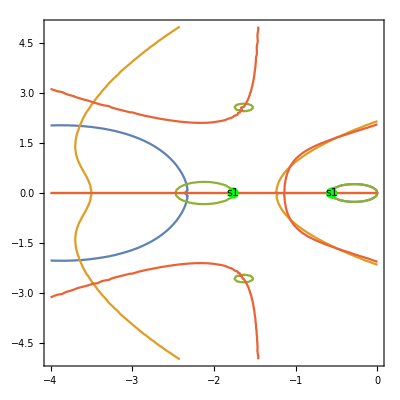

```mathematica
Pplot=Exp[δ] ParabolicCylinderD[-ll,(μ-vr)/Sqrt[d]]/ParabolicCylinderD[-ll,(μ-vt)/Sqrt[d]]/.param;

Papp=1/polynome[ll];




pts={{-1.7663681588617726,0},{-0.5608492562743866,0}};
ContourPlot[{Re[Pplot]==1,Im[Pplot]==0,Re[Papp]==1,Im[Papp]==0},{a,-4,0},{b,-5,5},Epilog->{PointSize[0.02],Green,Point[#]&/@pts,Black,Text["s1",#]&/@pts}]
```

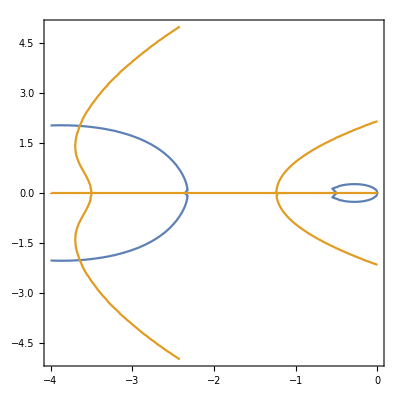

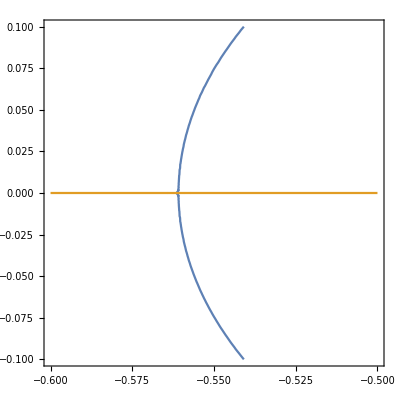

```mathematica
ContourPlot[{Re[Pplot]==1,Im[Pplot]==0},{a,-4,0},{b,-5,5}]

ContourPlot[{Re[Papp]==1,Im[Papp]==0,0},{a,-.6,-.5},{b,-0.1,0.1}]
```

```mathematica
Plot3D[{Re[(Pplot)],Re[(Papp)]},{a,-4,0},{b,-5,5}]
Plot3D[{Re[(Pplot)]},{a,-4,0},{b,-5,5}]
Plot3D[{Re[(Papp)]},{a,-.6,-.5},{b,-0.1,0.1}]
Plot3D[{Im[(Pplot)],Im[(Papp)]},{a,-4,0},{b,-5,5}]
Plot3D[{Im[(Pplot)]},{a,-4,0},{b,-5,5}]
Plot3D[{Im[(Papp)]},{a,-4,0},{b,-5,5}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»